## Chapter 9: Neural Networks with the Wolfram Language

## 9.1 Layers

### 9.1.1 Layers

### 9.1.2 Input Data

### 9.1.3 Linear Layer

```mathematica
LinearLayer["Input"->1,"Output"->2]
```

LinearLayer[…]

### 9.1.4 Weights and Biases

```mathematica
LinearLayer["Input"->{2,"Real"},"Output"->{3,2}]
```

LinearLayer[…]

```mathematica
LinearLayer["Input"-> 1,"Output"-> 1,"Weights"-> 1,"Biases"-> 2]
```

LinearLayer[…]

### 9.1.3 Initializing a Layer

```mathematica
NetInitialize[LinearLayer["Input"-> "Real","Output"-> "Real",LearningRateMultipliers->{"Biases"->1}]]
```

LinearLayer[…]

```mathematica
NetInitialize[LinearLayer["Input"-> "Real","Output"-> "Real",LearningRateMultipliers->{"Biases"->1}],Method-> {"Xavier","Distribution"->"Normal"},RandomSeeding->888]
```

LinearLayer[…]

### 9.1.5 Retrieving Data

```mathematica
linearL=NetInitialize[LinearLayer[2, "Input"-> 1],RandomSeeding->888];
NetExtract[linearL,#]&/@{"Weights","Biases"}//TableForm
```

NumericArray[…]
NumericArray[…]

```mathematica
TableForm[SetPrecision[{{Normal[NetExtract[linearL,"Weights"]]},{Normal[NetExtract[linearL,"Biases"]]}},3],TableHeadings->{{"Weights →","Biases →"},None}]
```

Weights → | -0.779
0.0435
Biases → | 0
0

```mathematica
linearL[4]
```

{-3.11505,0.174007}

```mathematica
linearL[{88,99}]
```

LinearLayer::invindata1: Data supplied to port "Input" was a length-2 vector of real numbers, but expected a length-1 vector.

$Failed

```mathematica
linearL[2,NetPortGradient["Input"]]
```

{-0.735261}

### 9.1.6 Mean Squared Layer

```mathematica
MeanSquaredLossLayer[]
```

MeanSquaredLossLayer[…]

```mathematica
MeanSquaredLossLayer["Input"->{3,2},"Target"->{3,2}][Association["Input"->{{1,2},{2,1},{3,2}},"Target"->{{2,2},{1,1},{1,3}}]]
```

1.16667

```mathematica
lossLayer=MeanSquaredLossLayer["Input"->{3,2},"Target"->{3,2} ];
lossLayer@<|"Input"->{{1,2},{2,1},{3,2}},"Target"->{{2,2},{1,1},{1,3}}|>
```

1.16667

```mathematica
Information[lossLayer]
```

Net Information

```mathematica
MeanSquaredLossLayer["Input"->"Real","Target"->"Real"]//Options
```

{BatchSize→Automatic,NetEvaluationMode→Test,RandomSeeding→Automatic,TargetDevice→CPU,WorkingPrecision→Real32}

```mathematica
{MeanSquaredLossLayer["Input"->"Varying","Target"->"Varying"],MeanSquaredLossLayer["Input"-> NetEncoder["Image"],"Target"-> NetEncoder["Image"]],MeanSquaredLossLayer["Input"->1,"Target"->1]}//Dataset
```

### 9.1.7 Activation Functions

```mathematica
ElementwiseLayer[Tanh[#]&](* Altnernate form ElementwiseLayer[Tanh]*)
```

ElementwiseLayer[…]

```mathematica
ElementwiseLayer[Tanh[#]&];
Table[%[i],{i,-5,5}]
```

{-0.999909,-0.999329,-0.995055,-0.964028,-0.761594,0.,0.761594,0.964028,0.995055,0.999329,0.999909}

```mathematica
tanhLayer=ElementwiseLayer[Tanh,"Input"-> "Real"]
```

ElementwiseLayer[…]

```mathematica
rampLayer=ElementwiseLayer[Ramp,"Output"-> {1}](*or ElementwiseLayer["ReLU","Output"-> "Varying"]*)
```

ElementwiseLayer[…]

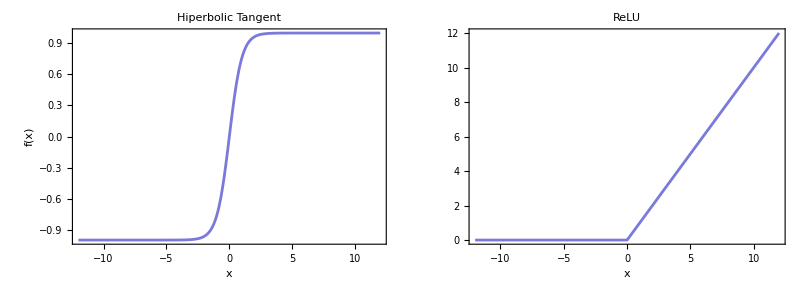

```mathematica
GraphicsRow@{Plot[tanhLayer[x,TargetDevice-> "CPU"],{x,-12,12},PlotLabel->"Hiperbolic Tangent",AxesLabel->{Style["x",Bold,12],Style["f(x)",Italic]},PlotStyle->ColorData[97,25],Frame->True],Plot[rampLayer[x,TargetDevice->"CPU"],{x,-12,12},PlotLabel->"ReLU",
AxesLabel->{None,Style["f(x)",Italic]},
FrameLabel->{{None,None},{Style["x",Bold,12],None}},PlotStyle->ColorData[97,25],Frame->True]}
```

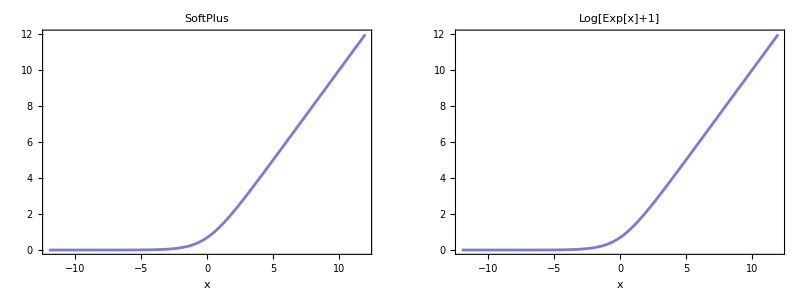

```mathematica
GraphicsRow@{Plot[ElementwiseLayer["SoftPlus"][x,TargetDevice->"CPU"],{x,-12,12},PlotLabel->"SoftPlus",AxesLabel->{None,Style["f(x)",Italic]},
FrameLabel->{{None,None},{Style["x",Bold,12],None}},PlotStyle->ColorData[97,25],Frame->True],Plot[Log[Exp[x]+1],{x,-12,12},PlotLabel->"Log[Exp[x]+1]",AxesLabel->{None,Style["f(x)",Italic]},
FrameLabel->{{None,None},{Style["x",Bold,12],None}},PlotStyle->ColorData[97,25],Frame->True]}
```

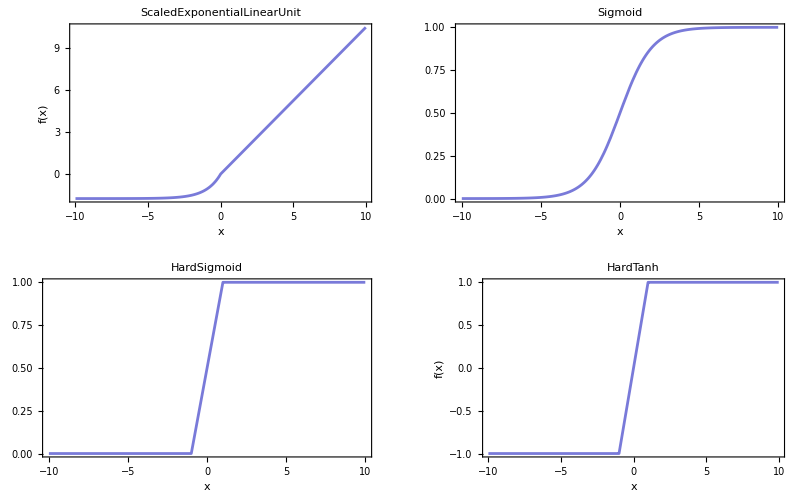

```mathematica
GraphicsGrid@Partition[Table[If[Or[activation=="Sigmoid",activation=="HardSigmoid"],Plot[ElementwiseLayer[activation][x,TargetDevice->"CPU"],{x,-10,10},FrameLabel->{Style["x",Bold],None},AxesLabel->{None,Style["f(x)",Italic]},PlotStyle->ColorData[97,25],Frame->True,PlotLabel->activation],Plot[ElementwiseLayer[activation][x,TargetDevice->"CPU"],{x,-10,10},AxesLabel->{Style["x",Bold],Style["f(x)",Italic]},PlotStyle->ColorData[97,25],Frame->True,PlotLabel->activation]],{activation,{"ScaledExponentialLinearUnit","Sigmoid","HardSigmoid","HardTanh"}}],2]
```

### 9.1.8 SoftMax Layer

```mathematica
sFL=SoftmaxLayer["Input"-> 4,"Output"-> 4];
```

```mathematica
SetAccuracy[SFL[{9,8,7,6}],3]
```

{0.64,0.24,0.09,0.03}

```mathematica
SoftmaxLayer[1,"Input"->{3,2}];
SetPrecision[%[{{7,8},{8,7},{7,8}}],3]//MatrixForm
```

(0.212 | 0.422
0.576 | 0.155
0.212 | 0.422)

```mathematica
CrossEntropyLossLayer["Probabilities","Input"->3 ];
```

```mathematica
%[<|"Input"->{0.2,0.5,0.3},"Target"->{0.3,0.5,0.2}|>]
```

1.0702

```mathematica
CrossEntropyLossLayer["Binary","Input"-> 1];
%[<|"Input"-> 0.1,"Target"-> 0.9|>]
```

2.08286

### 9.1.9 Function Layer

```mathematica
FunctionLayer[#*2&]
```

FunctionLayer[…]

```mathematica
FunctionLayer[1/(1+Exp[-#])&];
%[{2,-3,4}]
```

{0.880797,0.0474259,0.982014}

```mathematica
FunctionLayer[LogisticSigmoid];
%[{2,-3,4}]
```

{0.880797,0.0474259,0.982014}

## 9.2 Encoder and Decoders

### 9.2.1 Encoder

```mathematica
NetEncoder["Boolean"]
```

NetEncoder[…]

```mathematica
Print["Booleans:",{%[True],%[False]}]
```

Booleans:{1,0}

```mathematica
NetEncoder[{"Class",{"Class X","Class Y"}}]
```

NetEncoder[…]

```mathematica
Print["Classes:",%[Table[RandomChoice[{"Class X","Class Y"}],{i,10}]]]
```

Classes:{2,2,2,1,1,1,1,1,2,2}

```mathematica
NetEncoder[{"Class",{"Class X","Class Y","Class Z"},"UnitVector"}];
Print["Unit Vector:",%[Table[RandomChoice[{"Class X","Class Y","Class Z"}],{i,5}]]]
Print["MatrixForm:",%%[Table[RandomChoice[{"Class X","Class Y","Class Z"}],{i,5}]]//MatrixForm[#]&]
```

Unit Vector:{{0,1,0},{0,0,1},{0,1,0},{0,1,0},{0,1,0}}

MatrixForm:(0 | 1 | 0
0 | 1 | 0
0 | 1 | 0
0 | 0 | 1
1 | 0 | 0)

```mathematica
ElementwiseLayer[Sin,"Input"->NetEncoder["Boolean"]]
```

ElementwiseLayer[…]

```mathematica
LinearLayer["Input"->NetEncoder[{"Class",{"Class X","Class Y"}}],"Output"->"Scalar"]
```

LinearLayer[…]

```mathematica
Table[NetEncoder[{"Image",{28,28},"ColorSpace"-> Color}],{Color,{"Grayscale","RGB"}}]
```

{NetEncoder[…],NetEncoder[…]}

```mathematica
imgEncoder=NetEncoder[{"Image",{3,3},"ColorSpace"-> "CMYK"}];
Print["Numeric Matrix:",SetPrecision[%[ExampleData[{"TestImage","House"}]],3]//MatrixForm]
```

Numeric Matrix:((0.255
0.169
0.255) | (0.145
0.00392
0.0235) | (0.0784
0.0118
0.0275)
(0.153
0.196
0.129) | (0.2
0.31
0.255) | (0.259
0.349
0.306)
(0.0471
0.102
0.00784) | (0.165
0.322
0.165) | (0.263
0.384
0.176)
(0.161
0.263
0.184) | (0.255
0.408
0.478) | (0.325
0.388
0.569))

### 9.2.2 Pooling Layer

```mathematica
poolLayer=PoolingLayer[{3,3},{2,2},PaddingSize->0,"Function"-> Max,"Input"-> NetEncoder[{"Image",{3,3},"ColorSpace"-> "CMYK"}](*Or ImgEncoder*)]
```

PoolingLayer[…]

```mathematica
SetPrecision[poolLayer[ExampleData[{"TestImage","House"}]],3]//MatrixForm
```

((0.255)
(0.349)
(0.384)
(0.569))

### 9.2.3 Decoders

```mathematica
decoder=NetDecoder[{"Class",CharacterRange["W","Z"]}]
```

NetDecoder[…]

```mathematica
decoder@{0.3,0.2,0.1,0.4}(*This is the same as Decoder[{0.3,0.2,0. 1,0,4},"Decision"]*)
```

Z

```mathematica
TableForm[{decoder[{0.3,0.2,0.1,0.4},"TopDecisions"-> 4](* or {"TopDecisions", 4} the same is for TopProbabilities*),
decoder[{0.3,0.2,0.1,0.4},"TopProbabilities"->  4],
decoder[{0.3,0.2,0.1,0.4},"Entropy"]},TableDirections->Column,TableHeadings->{{Style["TopDecisions",Italic],Style["TopProbabilities",Italic],Style["Entropy",Italic]},None}]
```

TopDecisions | Z | W | X | Y
TopProbabilities | Z→0.4 | W→0.3 | X→0.2 | Y→0.1
Entropy | 1.27985 |  |  |

```mathematica
NetDecoder[{"Class",CharacterRange["X","Z"],"InputDepth"->2}];
```

```mathematica
TableForm[{%[{{0.1,0.3,0.6},{0.3,0.4,0.3}},"TopDecisions"-> 3](* or {"TopDecisions", 4} the same is for TopProbabilities*),
%[{{0.1,0.3,0.6},{0.3,0.4,0.3}},"TopProbabilities"->  3],
%[{{0.1,0.3,0.6},{0.3,0.4,0.3}},"Entropy"]},TableDirections->Column,TableHeadings->{{Style["TopDecisions",Italic],Style["TopProbabilities",Italic],Style["Entropy",Italic]},None}]
```

TopDecisions | Z
Y
X | Y
X
Z
TopProbabilities | Z→0.6
Y→0.3
X→0.1 | Y→0.4
X→0.3
Z→0.3
Entropy | 0.897946 | 1.0889

```mathematica
SoftmaxLayer["Output"->NetDecoder[{"Class",{"X","Y","Z"}}]];
```

```mathematica
{%@{1,3,5},%[{1,3,5},"Probabilities"],%[{1,3,5},"Decision"]}
```

{Z,<|X→0.0158762,Y→0.11731,Z→0.866813|>,Z}

### 9.2.4 Applying Encoder and Decoders

```mathematica
img=ImageResize[ExampleData[{"TestImage","House"}],200]
```

-Graphics-

```mathematica
encoder=NetEncoder[{"Image",{100,100},"ColorSpace"-> "RGB"}];
decoder=NetDecoder[{"Image",ColorSpace-> "Grayscale"}];
```

```mathematica
encoder[img];
decoder[%]
```

-Graphics-

```mathematica
ImageDimensions[%]
```

{100,100}

## 9.3 NetChain and Graphs

### 9.3.1 Containers

```mathematica
NetChain[{ElementwiseLayer[LogisticSigmoid@#&],ElementwiseLayer[Sin@#&]}]
```

NetChain[…]

```mathematica
NetInitialize@NetChain[{3,4,12,Tanh},"Input"->1]
```

NetChain[…]

```mathematica
NetInitialize@NetChain[{1,ElementwiseLayer[LogisticSigmoid@#&]},"Input"-> 1];
netCH2=NetInitialize@NetAppend[%,{1,ElementwiseLayer[Cos[#]&]}]
```

NetChain[…]

```mathematica
netCH2[{{0},{2},{44}},NetEvaluationMode-> "Train",TargetDevice->"CPU",WorkingPrecision-> "Real64",RandomSeeding-> 8888](*use N@Cos[Sin[LogisticSigmoid[{0,2,44}]]] to check results*)
```

{{0.967873},{0.990894},{1.}}

```mathematica
NetInitialize@NetChain[<|"Linear Layer 1"->LinearLayer[3],
"Ramp"-> Ramp,"Linear Layer 2"->LinearLayer[4],"Logistic"-> ElementwiseLayer[LogisticSigmoid]|>,"Input"-> 3]
```

NetChain[…]

```mathematica
NetExtract[%,"Logistic"];
```

```mathematica
Normal[netCH2]//Column
```

LinearLayer[…]
ElementwiseLayer[…]
LinearLayer[…]
ElementwiseLayer[…]

### 9.3.2 Multiple Chains

```mathematica
chain1=NetChain[{12,SoftmaxLayer[]}];
chain2=NetChain[{1,ElementwiseLayer[Cos[#]&]}];
nestedChain=NetInitialize@NetChain[{chain1,chain2},"Input"-> 12]
```

NetChain[…]

```mathematica
NetFlatten[nestedChain]
```

NetChain[…]

### 9.3.3 NetGraphs

```mathematica
NetInitialize@NetGraph[{ LinearLayer["Output"-> 1,"Input"-> 1],Cos,SummationLayer[]},{}]
```

NetGraph[…]

```mathematica
net1=NetInitialize@NetGraph[{ LinearLayer["Output"-> 2,"Input"-> 1],Cos,SummationLayer[]},{1-> 2-> 3}]
```

NetGraph[…]

```mathematica
net2=NetInitialize@NetGraph[{ LinearLayer["Output"-> 2,"Input"-> 1],Cos,SummationLayer[]},{1-> 3->2}]
```

NetGraph[…]

```mathematica
NetInitialize@NetGraph[<|"Layer 1"-> LinearLayer[2,"Input"-> 1],"Layer 2"-> Cos,"Layer 3"-> SummationLayer[]|>,{"Layer 2"-> "Layer 1"-> "Layer 3"}]
```

NetGraph[…]

```mathematica
NetInitialize@NetGraph[{ LinearLayer[3,"Input"-> 1],  LinearLayer[3,"Input"-> 2], LinearLayer[3,"Input"-> 1] ,TotalLayer[]},{NetPort["1st Input"]-> 1, NetPort["2nd Input"]-> 2,NetPort["3rd Input"]-> 3,{1,2,3}-> 4}](*Or NetInitialize@NetGraph[<|"L1"->  LinearLayer[3,"Input"-> 1],"L2"->   LinearLayer[3,"Input"-> 1], "L3"-> LinearLayer[3,"Input"-> 1] ,"Tot L"-> TotalLayer[]|>,{NetPort["1st Input"]-> "L1", NetPort["2nd Input"]-> "L2",NetPort["3rd Input"]->"L3",{"L1","L2","L3"} -> "Tot L"}]*)
```

NetGraph[…]

```mathematica
%[<|"1st Input"-> 32.32,"2nd Input"-> {2,π},"3rd Input"-> 1|>]
```

{82.4758,-42.202,-37.4852}

```mathematica
NetInitialize[NetGraph[{LinearLayer[1,"Input"-> 1],LinearLayer[1,"Input"-> 1],LinearLayer[1,"Input"-> 1],Ramp,ElementwiseLayer["ExponentialLinearUnit"],LogisticSigmoid},{1->4-> NetPort["Output1"],2->5-> NetPort["Output2"],3-> 6-> NetPort["Output3"]}],RandomSeeding->8888]
%[{1}]
```

NetGraph[…]

<|Output1→{0.},Output2→{-0.289052},Output3→{0.860635}|>

```mathematica
NetInitialize@NetGraph[{
LinearLayer[1,"Input"-> 1],
NetChain[{LinearLayer[1,"Input"-> 1],ElementwiseLayer[LogisticSigmoid[#]&]}],
NetChain[{LinearLayer[1,"Input"-> 1],Ramp}],
ElementwiseLayer["ExponentialLinearUnit"],
CatenateLayer[]
},{1->4,2->5,3-> 5,4-> 5}]
```

NetGraph[…]

### 9.3.4 Combining Containers

```mathematica
N1=NetGraph[{1,Ramp,2,LogisticSigmoid},{1-> 2,2-> 3,3-> 4}];
N2=NetChain[{3,SummationLayer[]}];
NetInitialize@NetGraph[{N2,N1},{2-> 1},"Input"-> 22]
```

NetGraph[…]

```mathematica
net=NetInitialize@NetGraph[{LinearLayer[10],Ramp,10,SoftmaxLayer[],TotalLayer[],ThreadingLayer[Times]},{1->2->3->4,{1,2,3}->5,{1,5}->6},"Input"->"Real"];
Information[net,"SummaryGraphic"]
```

-Graphics-

### 9.3.5 Network Properties

```mathematica
{Dataset@Information[net,"Arrays"],Dataset@Information[net,"ArraysDimensions"],Dataset@Information[net,"ArraysPositionList"]}
```

{,,}

```mathematica
{Information[net,"InputPorts"],Information[net,"OutputPorts"]}
```

{<|Input→Real|>,<|Output1→10,Output2→10|>}

```mathematica
Dataset@{Information[net,"Layers"],Information[net,"LayerTypeCounts"]}
```

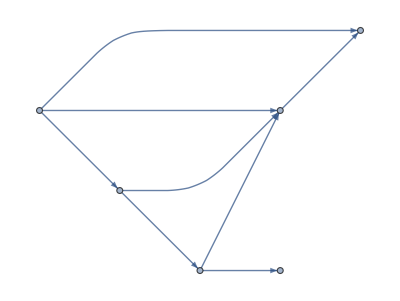
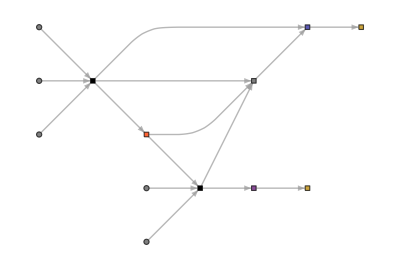
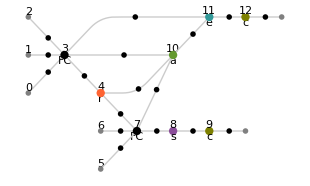
Layers Connection | NetGraph
-Graphics- | -Graphics-
MXNet Layer Graph | MXNet Ops Graph
-Graphics- | -Graphics-

```mathematica
Grid[{{Style["Layers Connection",Italic,20,ColorData[105,4]],Style["NetGraph",Italic,20,ColorData[105,4]]},{Information[net,"LayersGraph"],Information[net,"SummaryGraphic"]},
{Style["MXNet Layer Graph",Italic,20,ColorData[105,4]],Style["MXNet Ops Graph",Italic,20,ColorData[105,4]]},
{Information[net,"MXNetNodeGraph"],Information[net,"MXNetNodeGraphPlot"]}},Dividers->All,Background->{{{None,None}},{{Opacity[1,Gray],None}}}]
```

### 9.3.6 Exporting and Importing a Model

```mathematica
fileDirectory="/Users/macosx/Desktop";
Export[FileNameJoin[{fileDirectory,"MxNet.json"}],net,"MXNet","ArrayPath"-> Automatic,"SaveArrays"-> True]
```

/Users/macosx/Desktop/MxNet.json

```mathematica
FileNames[All,File@fileDirectory]
```

{/Users/macosx/Desktop/ABARROTES.txt,/Users/macosx/Desktop/.DS_Store,/Users/macosx/Desktop/Geant4_VM_Para,/Users/macosx/Desktop/Key Index Words.docx,/Users/macosx/Desktop/MxNet.json,/Users/macosx/Desktop/MxNet.params,/Users/macosx/Desktop/proton_recovery_ALBERT.asc,/Users/macosx/Desktop/proton_recovery_BTZ37.asc,/Users/macosx/Desktop/SUBIR_EL_1_MARZO_VIERNSE,/Users/macosx/Desktop/Tasks_Monday_Dec_04_2023.docx,/Users/macosx/Desktop/.vscode,/Users/macosx/Desktop/Wolfram_V2_Book}

```mathematica
Import[FileNameJoin[{FileDirectory,"MxNet.json"}],{"MXNet","NetExternalObject"},InputPorts-><|"Input"->{1}|>,"ArrayPath"->None];
```

```mathematica
Row[Dataset[Import[FileNameJoin[{FileDirectory,"MxNet.json"}],{"MXNet",#}]]&/@{"ArrayAssociation","ArrayList","ArrayNames"}]
```

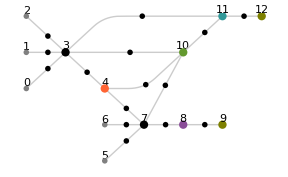

```mathematica
{Import[FileNameJoin[{FileDirectory,"MxNet.json"}],{"MXNet","NodeDataset"}],Import[FileNameJoin[{FileDirectory,"MxNet.json"}],{"MXNet","NodeGraphPlot"}]}//Row
```

```mathematica
NetModel["CapsNet Trained on MNIST Data"]
```

NetGraph[<8>, <12>]